```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
udata=ReadList["Geff.dat", {Number,Number}];
cdatah=ReadList["cdatah.txt",{Number,Number}];
```

```mathematica
rudata=Join[udata,cdatah];
```

```mathematica
u=Interpolation[rudata];
ru[r_]:=Piecewise[{{1,0≤r<0.01},{u[r],0.01<=r≤201.5},{1,r>201.5}}];
```

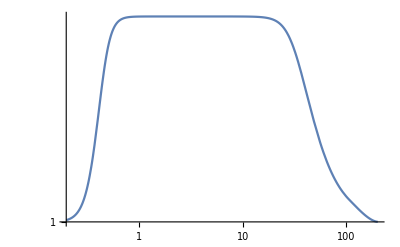

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
Ibdata=ReadList["Ibdata.txt",{Number,Number}];
```

```mathematica
rIb=Interpolation[Ibdata];
```

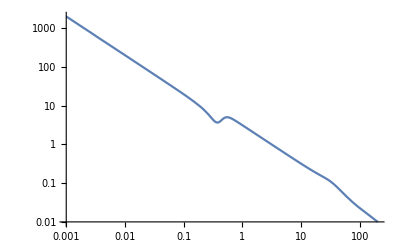

```mathematica
rrIb[b_]:=Piecewise[{{2/b,b<-201.5},{-rIb[-b],-201.5≤b≤-0.001},{2/b,-0.001<b<0.001},{rIb[b],0.001<=b≤201.5},{2/b,b>201.5}}];
LogLogPlot[rrIb[b],{b,0.001,201.5},PlotRange->All]
```

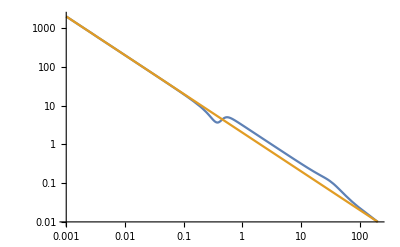

```mathematica
LogLogPlot[{rrIb[b],2/b},{b,0.001,201.5},PlotRange->All]
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^10;(*Msun*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

919.403

1653.06

1055.45

0.000694452

946.444

1701.68

1086.49

0.00067461

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
thetaEc=√((4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs]))
thetaE*DA[zl]
```

1.15224×10^-6

1.13566×10^-6

0.00105937

```mathematica
phihGR[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[-1/(√((DA[zl]*x)^2+z^2)),{z,0,Infinity}];
phihGRtest[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])Log[Abs[x]];
phihGRtest1[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[1/theta,{theta,10^-6,x}];
phiGRtest0[x_]=y[x]/.NDSolve[{y'[theta]==(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta,y[10^-6]==0},y,{theta,10^-7,10^-6},Method->"ExplicitRungeKutta"][[1]];
phihGRc[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs])Log[Abs[x]];
```

```mathematica
a[x_]:=Log[x];
```

```mathematica
phitest[x_]=y[x]/.NDSolve[{y'[r]==1/r,y[1]==0},y,{r,10^-10,1}];
```

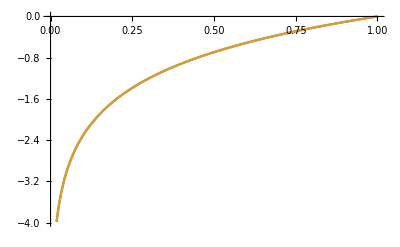

```mathematica
Plot[{a[x],phitest[x]},{x,0.0000001,1}]
```

```mathematica
phihMG[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[(-(1+ru[r])*ru[r])/(2*r)/.r->√((DA[zl]*x)^2+z^2),{z,0,Infinity}];
```

```mathematica
phiMGtest[x_]=y[x]/.NDSolve[{y'[theta]==DA2[zl,zs]/DA[zs]*(2*G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),y[10^-7]==0},y,{theta,10^-7,10^-6},Method->"ExplicitRungeKutta"][[1]];
phiMGtest1[x_]:=NIntegrate[DA2[zl,zs]/DA[zs]*(2*G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,10^-7,x}];
```

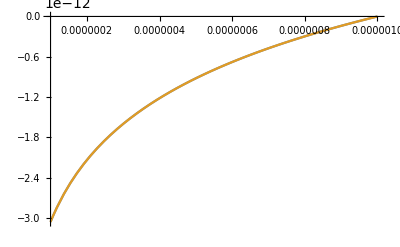

```mathematica
Plot[{phihGRtest[x]-phihGRtest[10^-6],phihGRtest1[x]},{x,10^-7,10^-6}]
```

```mathematica
phiMGtest1[x_]:=phiMGtest[Abs[x]];
```

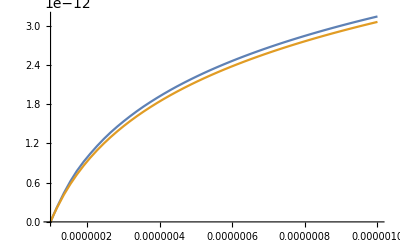

```mathematica
Plot[{phiMGtest[x],phiMGtest1[x]},{x,10^-7,10^-6}]
```